### Setup

```mathematica
options={MaxRecursion->100,AccuracyGoal->∞,WorkingPrecision->10};
```

```mathematica
markers = {{-Graphics-, 0.03}, {-Graphics-, 0.03}, {-Graphics-, 0.04}, {-Graphics-, 0.03}};
```

```mathematica
markers = {{-Graphics-, 0.03}, {-Graphics-, 0.03}};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Prior distributions

### Symmetry functions

```mathematica
ρ[θ_,η_]={{η Exp[- 1/θ],Sqrt[η(1-η)] Exp[- 1/(2θ)]},{Sqrt[η(1-η)] Exp[- 1/(2θ)],1-η Exp[- 1/θ]}};
ℒ[θ_,η_]=LyapunovSolve[ρ[θ,η],ρ[θ,η],2D[ρ[θ,η],θ]];
metric[θ_,η_]=Sqrt[Tr[ρ[θ,η].ℒ[θ,η].ℒ[θ,η]]]//FullSimplify;
```

```mathematica
pscale[θ_,θmin_,θmax_]:=1/(θ NIntegrate[1/x,{x,θmin,θmax}])
pmetric[θ_,θmin_,θmax_]:=metric[θ,1]/NIntegrate[metric[x,1],{x,θmin,θmax}]
```

### Measurement model

```mathematica
atomProbability[θ_]:=ProbabilityDistribution[x+  Exp[-1/θ](-1)^x,{x,0,1,1}]
```

### Construct estimate from dataset

```mathematica
estimateScale[data_,θmin_,θmax_]:=Module[
{tpθr={},test={},terror={},cont},

AppendTo[tpθr,1/θ(PDF[atomProbability[θ],x]/.x->data⟦1⟧)/NIntegrate[1/θ(PDF[atomProbability[θ],x]/.x->data⟦1⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test, Exp[NIntegrate[tpθr⟦1⟧Log[θ],{θ,θmin,θmax},Evaluate@options]]];
AppendTo[terror,test⟦1⟧√NIntegrate[tpθr⟦1⟧Log[test⟦1⟧/θ]^2,{θ,θmin,θmax},Evaluate@options]];
cont=0;
Monitor[Do[cont++;
AppendTo[tpθr,tpθr⟦k-1⟧(PDF[atomProbability[θ],x]/.x->data⟦k⟧)/NIntegrate[tpθr⟦k-1⟧(PDF[atomProbability[θ],x]/.x->data⟦k⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test,Exp[NIntegrate[tpθr⟦k⟧Log[θ],{θ,θmin,θmax},Evaluate@options]]];
AppendTo[terror,test⟦k⟧√NIntegrate[tpθr⟦k⟧Log[test⟦k⟧/θ]^2,{θ,θmin,θmax},Evaluate@options]];
,{k,2,Length[data]}],{100N[cont/Length[data]],ProgressIndicator[cont,{2,Length[data]}]}];
Return[Table[Around[test⟦i⟧,terror⟦i⟧],{i,Length[data]}]] 
]//Quiet
```

```mathematica
estimateMetric[data_,θmin_,θmax_]:=Module[
{tpθr={},test={},terror={},cont},

AppendTo[tpθr,√(1/((-1+ⅇ^(1/θ)) θ^4))(PDF[atomProbability[θ],x]/.x->data⟦1⟧)/NIntegrate[√(1/((-1+ⅇ^(1/θ)) θ^4))(PDF[atomProbability[θ],x]/.x->data⟦1⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test, 1/Log[Tan[NIntegrate[-tpθr⟦1⟧2 ArcTan[Sqrt[Exp[1/θ]-1]],{θ,θmin,θmax},Evaluate@options]/2]^2+1]];
AppendTo[terror,(-1+ⅇ^(1/test⟦1⟧))^(1/2) test⟦1⟧^2 √NIntegrate[tpθr⟦1⟧(-2 ArcTan[Sqrt[Exp[1/test⟦1⟧]-1]]+2 ArcTan[Sqrt[Exp[1/θ]-1]])^2,{θ,θmin,θmax},Evaluate@options]];
cont=0;
Monitor[Do[cont++;
AppendTo[tpθr,tpθr⟦k-1⟧(PDF[atomProbability[θ],x]/.x->data⟦k⟧)/NIntegrate[tpθr⟦k-1⟧(PDF[atomProbability[θ],x]/.x->data⟦k⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test, 1/Log[Tan[NIntegrate[-tpθr⟦k⟧2 ArcTan[Sqrt[Exp[1/θ]-1]],{θ,θmin,θmax},Evaluate@options]/2]^2+1]];
AppendTo[terror,(-1+ⅇ^(1/test⟦k⟧))^(1/2) test⟦k⟧^2 √NIntegrate[tpθr⟦k⟧(-2 ArcTan[Sqrt[Exp[1/test⟦k⟧]-1]]+2 ArcTan[Sqrt[Exp[1/θ]-1]])^2,{θ,θmin,θmax},Evaluate@options]];
,{k,2,Length[data]}],{100N[cont/Length[data]],ProgressIndicator[cont,{2,Length[data]}]}];
Return[Table[Around[test⟦i⟧,terror⟦i⟧],{i,Length[data]}]] 
]//Quiet
```

### Lifetime estimation

Superposition coefficient estimates

```mathematica
a=10;θmin=1/a;θmax=a;θtrue=0.26;μ=200;θest1={};θest2={};
Do[{data=RandomVariate[atomProbability[θtrue],μ],θestimates1=estimateScale[data,θmin,θmax],AppendTo[θest1,θestimates1[[μ]]],θestimates2=estimateMetric[data,θmin,θmax],AppendTo[θest2,θestimates2[[μ]]]},{i,1,10}]
```

Lifetime estimates

Save data

```mathematica
(*Export["θestimates1life.txt",θestimates1];
Export["θestimates2life.txt",θestimates2];
Export["θest1life.txt",θest1];
Export["θest2life.txt",θest2];*)
```

Import published estimates

```mathematica
μ=200;θtrue=1;
θestimates1=ToExpression/@StringSplit[Import["thestimates1life.txt","Text"],"\n"];
θestimates2=ToExpression/@StringSplit[Import["thestimates2life.txt","Text"],"\n"];
θest1=ToExpression/@StringSplit[Import["thest1life.txt","Text"],"\n"];
θest2=ToExpression/@StringSplit[Import["thest2life.txt","Text"],"\n"];
```

Variability

```mathematica
nsr1=Round[100Mean[(θest1[[All,1]]-Mean[θest1[[All,1]]])^2]/Mean[θest1[[All,1]]]^2,0.01]
nsr2=Round[100Mean[(θest2[[All,1]]-Mean[θest2[[All,1]]])^2]/Mean[θest2[[All,1]]]^2,0.01]
```

0.34

0.33

Plots

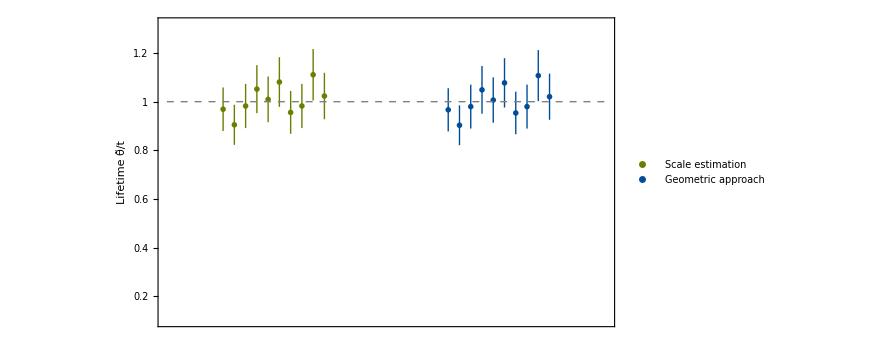

```mathematica
scatter1=Show[ListLinePlot[θestimates1⟦1;;μ⟧,PlotRange->All,PlotStyle->{RGBColor[0.4,0.5,0],Thick}, PlotMarkers->None,IntervalMarkers->"None",Frame->True,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->Directive["Times",21,Black],FrameLabel->{"Repetitions μ"},AspectRatio->0.45],ListLinePlot[θestimates1⟦1;;μ⟧,PlotRange->All,PlotStyle->{
RGBColor[0.4,0.5,0]}, PlotMarkers->None,IntervalMarkers->"Bands"],Plot[θtrue,{x,0,μ},PlotStyle->{Gray,Dashed, Thick}],PlotRange->{{1,μ-1},{0,5.3}},ImageSize->275,Epilog-> Inset[Style["(a)",21],Offset[{-3,-3},Scaled[{1,1}]],{Right,Top}]];
scatter2=Show[ListLinePlot[θestimates2⟦1;;μ⟧,PlotRange->All,PlotStyle-> {RGBColor[0,0.3,0.6],Thick},PlotMarkers->None,IntervalMarkers->"None",Frame->True,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->Directive["Times",21,Black],FrameLabel->{"Repetitions μ"},AspectRatio->0.45],ListLinePlot[θestimates2⟦1;;μ⟧,PlotRange->All,PlotStyle-> {RGBColor[0,0.3,0.6]},PlotMarkers->None,IntervalMarkers->"Bands"],Plot[θtrue,{x,0,μ},PlotStyle->{Gray,Dashed,Thick}],PlotRange->{{1,μ-1},{0,5.3}},ImageSize->275,Epilog-> Inset[Style["(b)",21],Offset[{-3,-3},Scaled[{1,1}]],{Right,Top}]];
Show[ListPlot[{Partition[Riffle[5+#&/@Range[-2,3,0.5],θest1],2],Partition[Riffle[15+#&/@Range[-2,3,0.5],θest2],2]},FrameStyle->Directive["Times",24,Black],PlotStyle->{RGBColor[0.4,0.5,0],RGBColor[0,0.3,0.6]},PlotMarkers->{"OpenMarkers",8},PlotLegends->Placed[LineLegend[{"Scale estimation", "Geometric approach"},LegendLayout->{"Row",1},LabelStyle->Directive["Times",21,Black]],{0.5,0.95}]],Plot[θtrue,{x,0.5,20},PlotStyle->{Gray,Dashed,Thick}],ImageSize->650,Epilog->{Inset[scatter1,ImageScaled[{0.34,0.3}]],Inset[scatter2,ImageScaled[{0.78,0.3}]]},Frame->True,Axes->False,FrameTicks->{{{{0,"0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1"},{1.2,"1.2"},{1.4,"1.4"}},{{0,""},{.2,""},{.4,""},{.6,""},{.8,""},{1,""},{1.2,""},{1.4,""}}},{None,None}},AspectRatio->0.55,FrameLabel->{None,"Lifetime θ̃/t"},PlotRange->{0.1,1.32}]
```

### Coherence estimation: small and sensitive sample

Superposition coefficient estimates

```mathematica
a=10;θmin=1/a;θmax=a;θtrue=0.26;μ=20;θest1={};θest2={};
Do[{data=RandomVariate[atomProbability[θtrue],μ],θestimates1=estimateScale[data,θmin,θmax],AppendTo[θest1,θestimates1[[μ]]],θestimates2=estimateMetric[data,θmin,θmax],AppendTo[θest2,θestimates2[[μ]]]},{i,1,10}]
```

Save data

```mathematica
(*Export["θestimates1lifeSensitive.txt",θestimates1];
Export["θestimates2lifeSensitive.txt",θestimates2];
Export["θest1lifeSensitive.txt",θest1];
Export["θest2lifeSensitive.txt",θest2];*)
```

Import published estimates

```mathematica
θestimates1=ToExpression/@StringSplit[Import["thestimates1lifeSensitive.txt","Text"],"\n"];
θestimates2=ToExpression/@StringSplit[Import["thestimates2lifeSensitive.txt","Text"],"\n"];
θest1=ToExpression/@StringSplit[Import["thest1lifeSensitive.txt","Text"],"\n"];
θest2=ToExpression/@StringSplit[Import["thest2lifeSensitive.txt","Text"],"\n"];
```

Variability

```mathematica
nsr1=Round[Sqrt[Mean[(θest1[[All,1]]-Mean[θest1[[All,1]]])^2]/Mean[θest1[[All,1]]]^2],0.01]
nsr2=Round[Sqrt[Mean[(θest2[[All,1]]-Mean[θest2[[All,1]]])^2]/Mean[θest2[[All,1]]]^2],0.01]
```

0.3

0.2

Plots

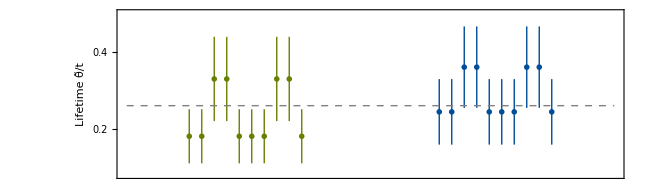

```mathematica
θtrue=0.26;μ=20;
Show[ListPlot[{Partition[Riffle[5+#&/@Range[-2,3,0.5],θest1],2],Partition[Riffle[15+#&/@Range[-2,3,0.5],θest2],2]},FrameStyle->Directive["Times",24,Black],PlotStyle->{RGBColor[0.4,0.5,0],RGBColor[0,0.3,0.6]},PlotMarkers->{"OpenMarkers",8}],Plot[θtrue,{x,0.5,20},PlotStyle->{Gray,Dashed,Thick}],ImageSize->650,Frame->True,Axes->False,FrameTicks->{{{{0,"0"},{.1,"0.1"},{.2,"0.2"},{.3,"0.3"},{.4,"0.4"},{.5,"0.5"}},{{0,""},{.1,""},{.2,""},{.3,""},{.4,""},{.5,""}}},{None,None}},AspectRatio->0.3,FrameLabel->{None,"Lifetime θ̃/t"},PlotRange->{0.08,0.5}]
```